ω_0

4.42945

α_theta

0.0648

α_phi

0.0648

a_u

0.3

a_v

0.

a_w

0.

β_u

1.1

β_v

1.1

β_w

4.4

P_theta

0.

P_phi

0.

Sin[θ[t]]+0.0648 θ'[t]-Cos[θ[t]] Sin[θ[t]] ϕ'[t]^2+θ''[t]==0.-0.363 Cos[1.1 t] Cos[θ[t]] Sin[ϕ[t]]

(0.0648 ϕ'[t])/(0.5-0.5 Cos[2 θ[t]])+2 Cot[θ[t]] θ'[t] ϕ'[t]+ϕ''[t]==0.-0.363 Cos[1.1 t] Cos[ϕ[t]] Csc[θ[t]]

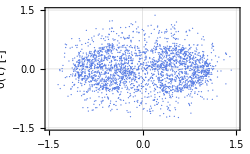

```mathematica
ClearAll["Global`*"] 

tend=14000;                       (* max time for the independent variable in ND Solve in s*)



l=0.5;                             (* Length of pendulum l*)
m=1.32;                        (*Mass at end of Pendulum in kg*)
g=9.81;                           (*Gravitational Acceleration in m/s^2*)


Subscript[ω, n]= Sqrt[g/l]  ;       (*Frequency for Excitation close to Natural Frequency*)

freq=1.1*Subscript[ω, n];
Subscript[Ω, u]=freq  ;                           (*Frequency for Excitation for Coordinate System in Direction of u in 1/s*)
Subscript[Ω, v]= freq;                              (*Frequency for Excitation for Coordinate System in Direction of v in 1/s*)
Subscript[Ω, w]=2* freq   ;                    (*Frequency for Excitation for Coordinate System in Direction of w in 1/s*)


Subscript[U, 0]=0.15;                        (*Amplitude u in m   *)
Subscript[V, 0]=0.0;                          (*Amplitude v in m*)
Subscript[W, 0]=0.0;                             (*Amplitude w in m*) 




(*Passive Damping*)

Subscript[ζ, θ] =0.0324;                                (*Damping coefficient no unit *)
Subscript[ζ, ϕ] =0.0324;                                (*Damping coefficient no unit*)





(*Active power take off*)

Subscript[T, θ]=0.0;                               (*Torque take off in Nm  swicht on with delay If[t<10,0.0,0.2]*)
Subscript[T, ϕ]=0.0    ;                                  (*Torque take off in Nm*)


"ω_0"
Subscript[ω, 0]=Sqrt[g/l]


"α_theta"
Subscript[α, theta]=2 Subscript[ζ, θ] Subscript[ω, n]/Subscript[ω, 0]
"α_phi"
Subscript[α, phi]=2 Subscript[ζ, ϕ] Subscript[ω, n]/Subscript[ω, 0]




"a_u"
Subscript[a, u]=Subscript[U, 0]/l

"a_v"
Subscript[a, v]=Subscript[V, 0]/l

"a_w"
Subscript[a, w]=Subscript[W, 0]/l



"β_u"
Subscript[β, u]=Subscript[Ω, u]/Subscript[ω, 0]
"β_v"
Subscript[β, v]=Subscript[Ω, v]/Subscript[ω, 0]
"β_w"
Subscript[β, w]=2*Subscript[Ω, w]/Subscript[ω, 0]




"P_theta"
Subscript[P, theta]=Subscript[T, θ]/(m l^2 Subscript[ω, 0]^2)
"P_phi"
Subscript[P, phi]=Subscript[T, ϕ]/(m l^2 Subscript[ω, 0]^2)
(*Initial conditions   *)
icthe=0.42;           
icphi=0.42;                       
dicthe=0.42;                        
dicphi=0.42;                       

(*ODEs*)
eqn1dim=Sin[θ[t]]+Subscript[α, theta] θ'[t]-Cos[θ[t]] Sin[θ[t]] ϕ'[t]^2+θ''[t]==-Cos[t Subscript[β, u]] Cos[θ[t]] Sin[ϕ[t]] Subscript[a, u] Subscript[β, u]^2+Cos[t Subscript[β, v]] Cos[θ[t]] Cos[ϕ[t]] Subscript[a, v] Subscript[β, v]^2+Cos[t Subscript[β, w]] Sin[θ[t]] Subscript[a, w] Subscript[β, w]^2-(Subscript[P, theta] 2)/π(ArcTan[(θ'[t]/0.01)])


eqn2dim=(Subscript[α, phi] ϕ'[t])/(0.5-0.5 Cos[2 θ[t]])+2 Cot[θ[t]] θ'[t] ϕ'[t]+ϕ''[t]==-Cos[t Subscript[β, u]] Cos[ϕ[t]] Csc[θ[t]] Subscript[a, u] Subscript[β, u]^2-Cos[t Subscript[β, v]] Csc[θ[t]] Sin[ϕ[t]] Subscript[a, v] Subscript[β, v]^2-(Sign[ϕ'[t]] Subscript[P, phi])/(0.5-0.5 Cos[2 θ[t]])




(*Calculation Poincare section*)
res=Reap[sol=NDSolve[{eqn1dim,eqn2dim,θ[0]==icthe,ϕ[0]==icphi,θ'[0]==dicthe,ϕ'[0]==dicphi,WhenEvent[Mod[((Subscript[β, u]*freq)/Subscript[ω, 0])*t,2π]==0,If[t>800,Sow[{θ[t],θ'[t]}]]]},{θ,ϕ},{t,0,tend},MaxSteps->∞]][[-1,1]];

(*Plot*)
ListPlot[{res}, LabelStyle->{FontFamily->"Times New Roman",FontSize->11},PlotTheme->{"Scientific","BoldColor","ItalicLabels","Frame","Grid"},FrameLabel ->{"θ(τ) [-]","θ̇(τ) [-]"},PlotStyle->Small,ImageSize->250,PlotRange->{{-1.5,1.5},{-1.5,1.5}}]
```